Juan Zambrano
Question 1:
Part A1:
 A)

```mathematica
FirstOrderEq={
A'[t]==-k A[t],
A[0]==A0
};
SolFirstOrder=DSolve[FirstOrderEq,A[t],t][[1]]
A1[t_]=A[t]/.SolFirstOrder
```

{A[t]→A0 ⅇ^(-k t)}

A0 ⅇ^(-k t)

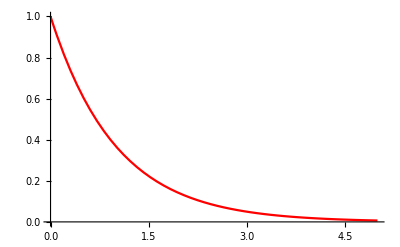

```mathematica
Subs1={k->1,A0->1};
PlotFirstOrder = Plot[{A1[t]} /. Subs1, {t,0,5},PlotStyle-> Red,FrameLabel->{{x,"Time(s)"},{y,"Concentration"}}]
```

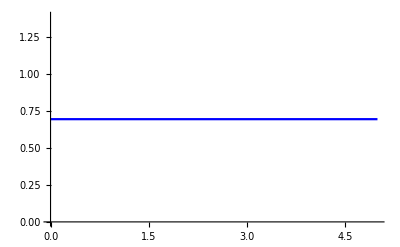

```mathematica
HalfLife = {
T[t] = Log[2]
};
PlotHalf = Plot[{T[t]}, {t,0,5},PlotStyle -> Blue]
```

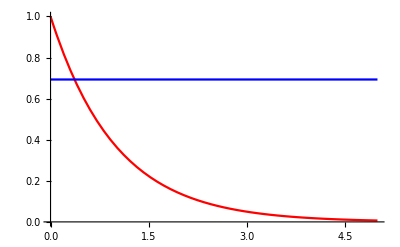

```mathematica
Show[PlotFirstOrder,PlotHalf]
```

The Red Plot above represents the Solution to the first order differential equation A‘[t] = -k A[t] , which is A[t]=A0 ⅇ^(-k t). The Blue plot represents the half life equation.  Assuming A0 and K = 1, we can treat the half-life of this reaction to be ln[2]. Using the Algebra expression we obtain a value of about 0.6931 for the half-life of the reaction. Plotting these two function we obtain the coordinates and value of about 0.6934 for the half-life. Therefore under these conditions, one can use the algebraic expression to approximate the half-life of a first order reaction. 
A second plot was generated to compare both half-life approximation methods but this time we changed the value of k to 10. Using the algebraic equation for half-life we obtained a half-life of 0.069. Therefore at this rate using the equation changes the half-life by a factor of 10.

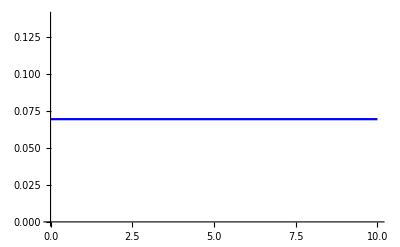

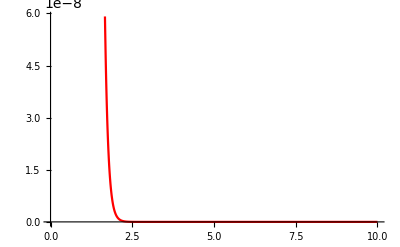

```mathematica
FirstOrderEq1={
A'[t]==-k A[t],
A[0]==A0
};
SolFirstOrder1=DSolve[FirstOrderEq,A[t],t][[1]]
A1[t_]=A[t]/.SolFirstOrder1;
Subs2={k->10,A0->1};
PlotFirstOrder1 = Plot[{A1[t]} /. Subs2, {t,0,10},PlotStyle-> Red,FrameLabel->{{x,"Time(s)"},{y,"Concentration"}}];
HalfLife2 = {
Y[t] = Log[2]/10
};
PlotHalf2 = Plot[{Y[t]}, {t,0,10},PlotStyle -> Blue]
Show[PlotFirstOrder1,PlotHalf2]
```

The half-life obtained from the graph is about 0.0694, which is in the same order of magnitude with the value obtained from the algebraic equation. In both scenarios the values obtained for the half-lifes is consistent no matter what the value of k is.

B)

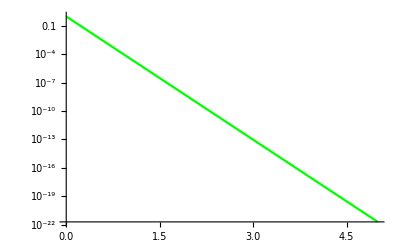

```mathematica
PlotLog = LogPlot[{A1[t]} /. Subs1, {t,0,5},PlotStyle-> Green]
```

The plot above represents the log of the plot from part a), which is Ln[A](t) = −k t + Ln[A0]. Taking the equation above and modeling like an algebraic Y=-mt + b, we can set Y = Ln[A](t) and b = Ln[A0]. Thus -mt = kt, therefore we can conclude that the slope(m) of this plot is equal to -k. Using the values of A0 = 1 and k = 1, we obtain a linear plot with intercept of zero, since Ln(A0) = Ln(1) = 0. Comparing these values to part a) we do indeed obtain the correct expected slope value.

A2:
a)

```mathematica
Eqns2={
A'[t]==-k A[t]^2,
A[0]==A0
};
Sol2=DSolve[Eqns2,A[t],t][[1]]
A2[t_]=A[t]/.Sol2
Subs2={k->0.5,A0->1};
Plot2=Plot[A2[t]/.Subs2,{t,0.05,5},PlotStyle->Pink]
```

b)
The first half-life of the second order reaction depicted above is 2.00. This value was obtained graphically and by using the equation t(half) = 1/k*A0

```mathematica
Eqns2Second={
A'[t]==-k A[t]^2,
A[0]==A0
};
Sol2Second=DSolve[Eqns2Second,A[t],t][[1]]
A2[t_]=A[t]/.Sol2
Subs2={k->0.5,A0->1/2};
Plot2=Plot[A2[t]/.Subs2,{t,0,5},PlotStyle->Pink]
```

The second half-life is depicted in the plot above where the intersection occurs. The second half-life of this second order reaction under the given conditions has a value of 4.00. 

c)

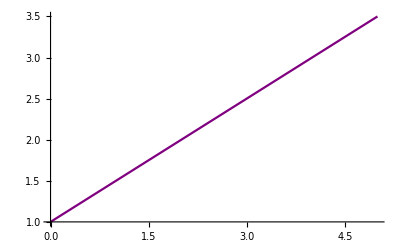

```mathematica
Eqns2Second={
A'[t]==-k A[t]^2,
A[0]==A0
};
Sol2Second=DSolve[Eqns2Second,A[t],t][[1]]
A2[t_]=A[t]/.Sol2
Subs2={k->0.5,A0->1};
Plot2=Plot[1/A2[t]/.Subs2,{t,0,5},PlotStyle->Purple]
```

Like the log plot in part A, The slope of this line describes the value of k. While the Y-intercept would be 1/A0. Plugging in the initial conditions of A0 = 1 and k = 0.5 we conclude that this plot is a valid model. Using the coordinates (x1 = 1.5,y1 = 2) and (x2= 2,y2 =2), we calculate the slope of the line and obtain 0.5 which is the parameter for k that we inputted in the code above.

d)

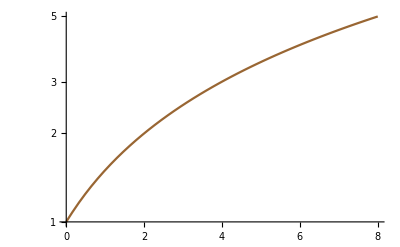

```mathematica
Plot2=LogPlot[1/A2[t]/.Subs2,{t,0,8},PlotStyle->Brown]
```

Unlike the First order rate law case, the log of a second order does not result in linear plot. 

A3:
a)

```mathematica
Rate1data=Import["/Users/juanzambrano/Desktop/Spring_2018/Compu Chem/rate1.dat.txt"];
```

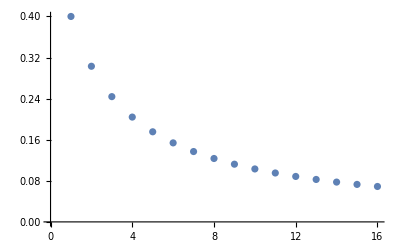

```mathematica
ListDataRate1 = { 0.4,0.30303,0.243902,0.204082,0.175439,0.153846,0.136986,0.123457,0.11236,0.103093,0.0952381,0.0884956,0.0826446,0.0775194,0.0729927,0.0689655};
ListPlot[ListDataRate1]
```

In  order to differentiate whether the data is first order or second order we Plot the log(concentration) vs. time and 1/concentration vs. time.
b)

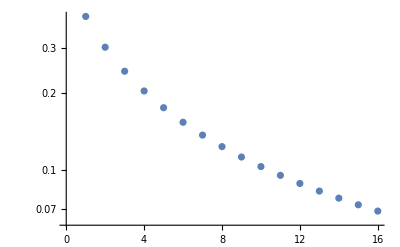

```mathematica
ListLogPlot[ListDataRate1]
```

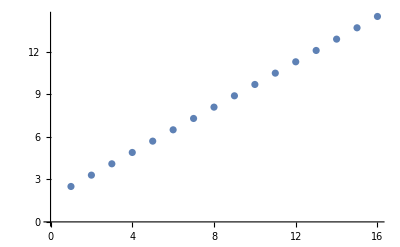

```mathematica
ListPlot[1/ListDataRate1]
```

After looking at the two Plots , we can determine that the 1/Concentration plot does result in a linear Plot, therefore the concentration data obtained was from a second order reaction.

C)

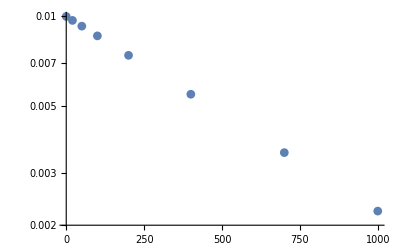

```mathematica
RateData2 = {{0.,0.01000},{20.,0.00970},{50.,0.00928},{100.,0.00861},{200.,0.00741},{400.,0.00549},{700.,0.00350},{1000.,0.00223}};
ListLogPlot[RateData2,PlotMarkers->Automatic]
```

From the Plot above we see that it is linear and therefore we do not need to conduct anymore test. We conclude that this data comes from a first order reaction.

D)
 In order to find the intercept and slope of the data I preform a linear regression on both sets of data.

```mathematica
SecondOrderRegression = LinearModelFit[1/ListDataRate1,x,x]
```

FittedModel[1.7+0.8 x]

```mathematica
FirstOrderRegression = Fit[LogLinearPlot[RateData2],{1,x},x]
```

Using a different software (excel) I was able to obtain the equation for the first order reaction. The slope of the line was -0.0015 and the intercept was -4.605. For the second order reaction I obtained a slope of 0.8 and an intercept of 1.7.
E)

Since the slope for datafile 2 is -0.0015, we can conclude that the rate constant is 0.0015.

```mathematica
Show[ListLogPlot[RateData2,PlotMarkers->Automatic],ListPlot[RateData2 ]]
```

-Graphics-

PART B:

B1:

```mathematica
Eqns1={
A'[t]==-k A[t],
A[0]==A0
};
Sol1=DSolve[Eqns1,A[t],t][[1]]
```

{A[t]→A0 ⅇ^(-k t)}

B2:

{A[t]→-1/(√(1/A0^2+2 k t))}

-1/(√(1/A0^2+2 k t))

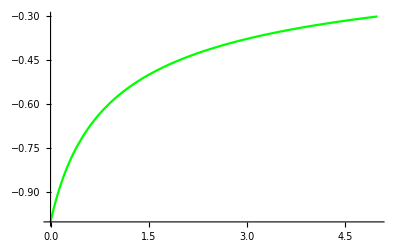

```mathematica
Eqns1={
A'[t]==-k A[t]^3,
A[0]==A0
};
Sol1=DSolve[Eqns1,A[t],t][[1]]
A1[t_]=A[t]/.Sol1
Subs1={k->1,A0->1};
Plot1=Plot[A1[t]/.Subs1,{t,0,5},PlotStyle->Green]
```

B3:
A)

```mathematica
Eqns7={
A'[t]==-k A[t](B[0] - A[0]+A[t]),
A[0]==A0
};
Sol3=DSolve[Eqns7,A[t],t][[1]]
Aconcentration[t_]=A[t]/.Sol3
```

{A[t]→-(ⅇ^((B[0] (Log[A0]-Log[A0+B[0]-A[0][0]]))/(B[0]-A[0][0])+k t A[t][0]) (B[0]-A[t][0]))/(ⅇ^((B[0] (Log[A0]-Log[A0+B[0]-A[0][0]]))/(B[0]-A[0][0])+k t A[t][0])-ⅇ^(k t B[0]+((Log[A0]-Log[A0+B[0]-A[0][0]]) A[t][0])/(B[0]-A[0][0])))}

-(ⅇ^((B[0] (Log[A0]-Log[A0+B[0]-A[0][0]]))/(B[0]-A[0][0])+k t A[t][0]) (B[0]-A[t][0]))/(ⅇ^((B[0] (Log[A0]-Log[A0+B[0]-A[0][0]]))/(B[0]-A[0][0])+k t A[t][0])-ⅇ^(k t B[0]+((Log[A0]-Log[A0+B[0]-A[0][0]]) A[t][0])/(B[0]-A[0][0])))

B)

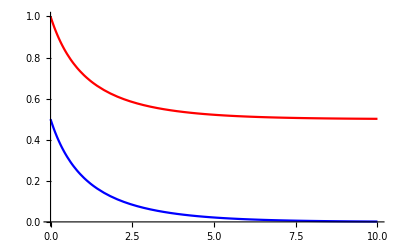

```mathematica
Eqnss={
A'[t]==-k A[t]B[t],
B'[t]==-k A[t]B[t],
A[0]==A0,
B[0]==B0
};
Subss={A0->1,B0->0.5,k->1};
Eqnss/.Subss;
Sols=NDSolve[Eqnss/.Subss,{A[t],B[t]},{t,0,10}][[1]];
Aconcen[t_]=A[t]/.Sols;
Bconcen[t_]=B[t]/.Sols;
Plot[{Aconcen[t],Bconcen[t]},{t,0,10},PlotStyle ->{Red,Blue}]
```

A cannot equal B in the solution because if they did then the resulting plot would be same.

B4:

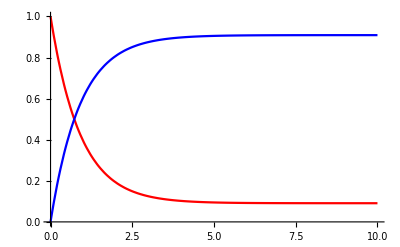

```mathematica
BackReaction={
A'[t]==-kf A[t]+kb X[t],
X'[t]==kf A[t]-kb X[t],
A[0]==A0,
X[0]==X0
};
BRsol=Simplify[DSolve[BackReaction,{A[t],X[t]},t][[1]]];
A3[t_]=A[t]/.BRsol;
X3[t_]=X[t]/.BRsol;
Subs3={A0->1,X0->0,kf->1,kb->.1};
Plot3=Plot[{A3[t]/.Subs3,X3[t]/.Subs3},{t,0,10},PlotStyle->{Red,Blue}]
```

using the values of 0.9 for concentration for the backwards reaction, since it plateau at that value and 0.1 for the forward value that it plateau at, we obtain a value for 9 for the equilibrium constant. Using the ratios of kf/kb we obtain a value of 10 which is pretty close to the value obtained using the previous method.

B5:
a)

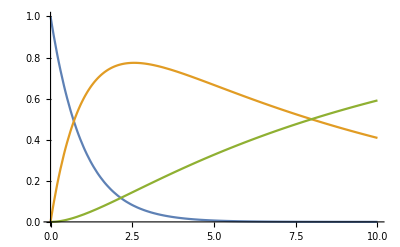

```mathematica
Eqns5={
A'[t]==-k1 A[t],
B'[t]==k1 A[t]-k2 B[t],
R'[t] == k2 B[t],
A[0]==A0,
B[0]==B0,
R[0] == R0
};
Subs5={A0->1,B0->0,R0 ->0,k1->1,k2 -> 0.1};
Eqns5 /. Subs5;
Sol5=DSolve[Eqns5/.Subs5,{A[t],B[t],R[t]},{t,0,10}][[1]];
An[t_]=A[t]/.Sol5;
Bn[t_]=B[t]/.Sol5;
Rn[t_] = R[t] /. Sol5;
Plot[{An[t],Bn[t],Rn[t]},{t,0,10}]
```

b)

ⅇ^-t

1/9 ⅇ^(-10 t) (-1+ⅇ^(9 t))

1/9 (9+ⅇ^(-10 t)-10 ⅇ^-t)

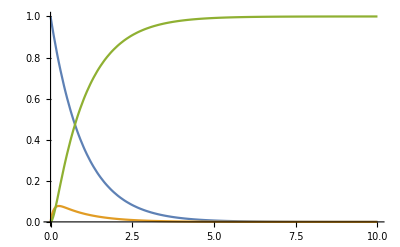

```mathematica
Eqns5={
A'[t]==-k1 A[t],
B'[t]==k1 A[t]-k2 B[t],
R'[t] == k2 B[t],
A[0]==A0,
B[0]==B0,
R[0] == R0
};
Subs5={A0->1,B0->0,R0 ->0,k1->1,k2 ->10};

Sol5=DSolve[Eqns5/.Subs5,{A[t],B[t],R[t]},{t,0,10}][[1]];
An[t_]=A[t]/.Sol5
Bn[t_]=B[t]/.Sol5
Rn[t_] = R[t] /. Sol5
Plot[{An[t],Bn[t],Rn[t]},{t,0,10}]
```

A larger concentration of B is produce therefore the concentration of product C is reduced, this implies that the ratio of the 2 rates is about 1:1 with some leakage that allows for a small amount of C to be produced.

B6:

0.0243902+0.94069 ⅇ^(-1.05584 t)+0.0349199 ⅇ^(-0.194158 t)

0.487805-1.0506 ⅇ^(-1.05584 t)+0.562799 ⅇ^(-0.194158 t)

0.487805+0.109914 ⅇ^(-1.05584 t)-0.597719 ⅇ^(-0.194158 t)

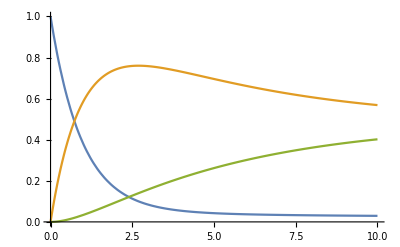

```mathematica
Eqns6={
A'[t]==-k1 A[t] + k3 B[t],
B'[t]==k1 A[t]-k3 B[t]-k2 B[t] + k4 R[t],
R'[t] == k2 B[t] - k4 R[t],
A[0]==A0,
B[0]==B0,
R[0] == R0
};
Subs6={A0->1,B0->0,R0 ->0,k1->1,k2 ->0.1,k3 ->0.05,k4 ->0.1};

Sol6=DSolve[Eqns6/.Subs6,{A[t],B[t],R[t]},{t,0,10}][[1]];
Ans[t_]=A[t]/.Sol6
Bns[t_]=B[t]/.Sol6
Rns[t_] = R[t] /. Sol6
Plot[{Ans[t],Bns[t],Rns[t]},{t,0,10}]
```

Adding these parameters changes the values for the concentrations by making them smaller. Graphically we still observe the same pattern, but as we can see adding the back reactions affects the concentration at a given time and reduces its value. Using this method results in a more accurate depiction of multiple step reactions.

B7:

```mathematica
Eqnsteady={
A'[t]==-k1 A[t] + k3 B[t],
0==k1 A[t]-k3 B[t]-k2 B[t] + k4 R[t],
R'[t] == k2 B[t] - k4 R[t],
A[0]==A0,
B[0]==B0,
R[0] == R0
};
Substeady={A0->1,B0->0,R0 ->0,k1->1,k2 ->0.1,k3 ->0.05,k4 ->0.1};
Eqnsteady /. Substeady;
Sol7=DSolve[Eqnsteady/.Substeady,{A[t],B[t],R[t]},{t,0,10}][[1]];
Ans[t_]=A[t]/.Sol7
Bns[t_]=B[t]/.Sol7
Rns[t_] = R[t] /. Sol7
Plot[{An[t],Bn[t],Rn[t]},{t,0,10}]
```

-Graphics-

Part C:

C1:

```mathematica
Eqns6={
A'[t]==-k1 A[t] + k3 B[t],
B'[t]==k1 A[t]-k3 B[t]-k2 B[t] + k4 R[t],
R'[t] == k2 B[t] - k4 R[t],
A[0]==A0,
B[0]==B0,
R[0] == R0
};
Subs6={A0->1,B0->0,R0 ->0,k1->1,k2 ->0.1,k3 ->0.05,k4 ->0.1};
Eqns6 /. Subs6;
Sol6=NDSolve[Eqns6/.Subs6,{A[t],B[t],R[t]},{t,0,10}][[1]];
Ans[t_]=A[t]/.Sol6
Bns[t_]=B[t]/.Sol6
Rns[t_] = R[t] /. Sol6
```

InterpolatingFunction[{{0., 10.}}, <>][t]

InterpolatingFunction[{{0., 10.}}, <>][t]

InterpolatingFunction[{{0., 10.}}, <>][t]

C2:

100

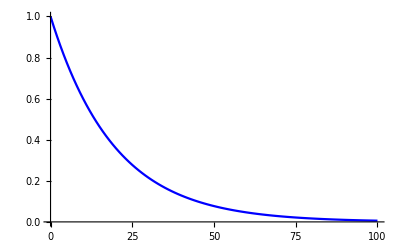

0.95

```mathematica
A0n=1;
kn=0.05;
tmax=100;
h=1.0;
nSteps=Round[tmax/h]
A[0]=A0n;
Do[
A[n+1]=A[n]-kn A[n]h,{n,0,nSteps}]
Adata=Table[{h n,A[n]},{n,0,nSteps}];
Firstt =ListPlot[Adata,Joined->True,PlotStyle->Blue]
An[Round[1/h]]
```

200

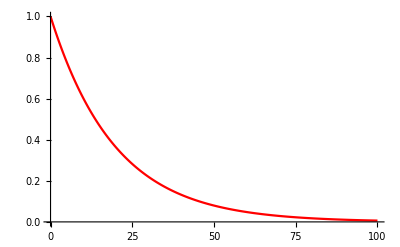

0.9025

```mathematica
A0n=1;
kn=0.05;
tmax=100;
h=0.5;
nSteps=Round[tmax/h]
A[0]=A0n;
Do[
A[n+1]=A[n]-kn A[n]h,{n,0,nSteps}]
Adata=Table[{h n,A[n]},{n,0,nSteps}];
Second =ListPlot[Adata,Joined->True, PlotStyle -> Red]
An[Round[1/h]]
```

2000

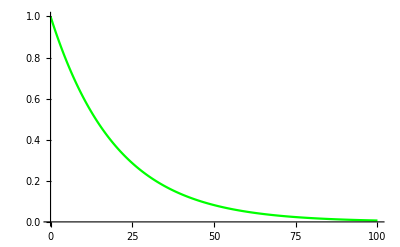

0.358486

```mathematica
A0n=1;
kn=0.05;
tmax=100;
h=0.05;
nSteps=Round[tmax/h]
A[0]=A0n;
Do[
A[n+1]=A[n]-kn A[n]h,{n,0,nSteps}]
Adata=Table[{h n,A[n]},{n,0,nSteps}];
Third =ListPlot[Adata,Joined->True, PlotStyle -> Green]
An[Round[1/h]]
```

10000

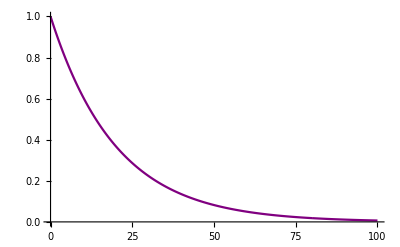

0.00592053

```mathematica
A0n=1;
kn=0.05;
tmax=100;
h=0.01;
nSteps=Round[tmax/h]
A[0]=A0n;
Do[
A[n+1]=A[n]-kn A[n]h,{n,0,nSteps}]
Adata=Table[{h n,A[n]},{n,0,nSteps}];
Fourth =ListPlot[Adata,Joined->True, PlotStyle -> Purple]
An[Round[1/h]]
```

Step sizes ranging from 2 to 0.01 were used for values of h. From theory we know that the concentration of this type of reaction at a given time is model by e^-kt,therefore using the parameters that were specified in the instructions, we tested different values of h and compared it to our calculations. Exp^[-(0.05)*(100)] = 0.00674. Starting at a step-size of 1, we were obtained a value of 0.95 for concentration at time 100s. After imputing more values for h , we found that the best value for the step size was to use a value of h = 0.01. This is the plot above which yields a concentration of 0.0059, which is about the same value that was predicted from e^-kt. The plot below represents all of the different values of h.

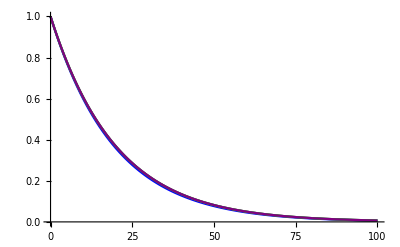

```mathematica
Show[Firstt,Second,Third,Fourth]
```

C3:

200

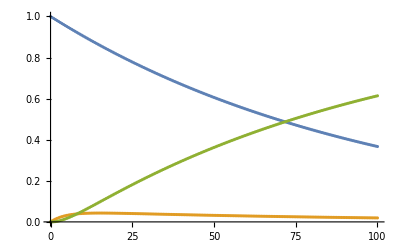

0.990025

```mathematica
k1n=0.01;
k2n=0.2;
A0n=1;
B0n=0;
C0n=0;
time=100;
h=0.5;
nSteps=Round[time/h]
An[0]=A0n;
Bn[0]=B0n;
Cn[0]=C0n;
Do[
An[n+1]=An[n]-h k1n An[n];
Bn[n+1]=Bn[n]+h k1n An[n]-h k2n Bn[n];
Cn[n+1]=Cn[n]+h k2n Bn[n];
,{n,0,nSteps}]
Adata=Table[{n h,An[n]},{n,0,nSteps}];
Bdata=Table[{n h,Bn[n]},{n,0,nSteps}];
Cdata=Table[{n h,Cn[n]},{n,0,nSteps}];
A1 =ListPlot[{Adata,Bdata,Cdata}]
An[Round[1/h]]
```

100

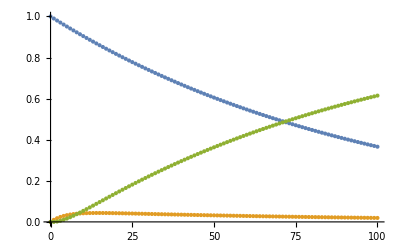

0.99

```mathematica
k1n=0.01;
k2n=0.2;
A0n=1;
B0n=0;
C0n=0;
time=100;
h=1;
nSteps=Round[time/h]
An[0]=A0n;
Bn[0]=B0n;
Cn[0]=C0n;
Do[
An[n+1]=An[n]-h k1n An[n];
Bn[n+1]=Bn[n]+h k1n An[n]-h k2n Bn[n];
Cn[n+1]=Cn[n]+h k2n Bn[n];
,{n,0,nSteps}]
Adata=Table[{n h,An[n]},{n,0,nSteps}];
Bdata=Table[{n h,Bn[n]},{n,0,nSteps}];
Cdata=Table[{n h,Cn[n]},{n,0,nSteps}];
B1 =ListPlot[{Adata,Bdata,Cdata}]
An[Round[1/h]]
```

50

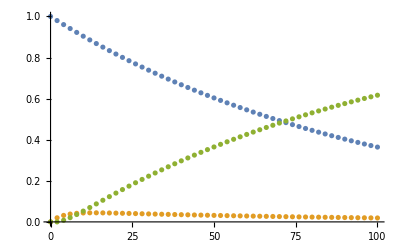

1

```mathematica
k1n=0.01;
k2n=0.2;
A0n=1;
B0n=0;
C0n=0;
time=100;
h=2;
nSteps=Round[time/h]
An[0]=A0n;
Bn[0]=B0n;
Cn[0]=C0n;
Do[
An[n+1]=An[n]-h k1n An[n];
Bn[n+1]=Bn[n]+h k1n An[n]-h k2n Bn[n];
Cn[n+1]=Cn[n]+h k2n Bn[n];
,{n,0,nSteps}]
Adata=Table[{n h,An[n]},{n,0,nSteps}];
Bdata=Table[{n h,Bn[n]},{n,0,nSteps}];
Cdata=Table[{n h,Cn[n]},{n,0,nSteps}];
C1 =ListPlot[{Adata,Bdata,Cdata}]
An[Round[1/h]]
```

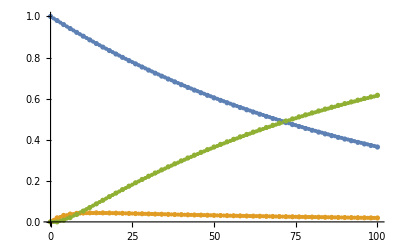

```mathematica
Show[A1,B1,C1,PlotStyle ->{Red,Blue,Green}]
```

As seen before the smaller the step-size the more accurate the results are. 

C4:

```mathematica
k1n=0.01;
k2n=0.2;
k3n = 0.15;
k4n = 0.1;
A0n=1;
B0n=0;
C0n=0;
time=100;
h=2;
nSteps=Round[time/h]
An[0]=A0n;
Bn[0]=B0n;
Cn[0]=C0n;
Do[
An[n+1]=An[n]-h k1n An[n] + h k3 Bn[n];
Bn[n+1]=Bn[n]+h k1n An[n]-h k2n Bn[n] - h k3 Bn[n] + h k4 Cn[n];
Cn[n+1]=Cn[n]+h k2n Bn[n] - h k4n Cn[n];
,{n,0,nSteps}]
Adata=Table[{n h,An[n]},{n,0,nSteps}];
Bdata=Table[{n h,Bn[n]},{n,0,nSteps}];
Cdata=Table[{n h,Cn[n]},{n,0,nSteps}];
D1 =ListPlot[{Adata,Bdata,Cdata}]
An[Round[1/h]]
```

50

```mathematica
k1n=0.01;
k2n=0.2;
k3n = 0.15;
k4n = 0.1;
A0n=1;
B0n=0;
C0n=0;
time=100;
h=1;
nSteps=Round[time/h]
An[0]=A0n;
Bn[0]=B0n;
Cn[0]=C0n;
Do[
An[n+1]=An[n]-h k1n An[n] + h k3 Bn[n];
Bn[n+1]=Bn[n]+h k1n An[n]-h k2n Bn[n] - h k3 Bn[n] + h k4 Cn[n];
Cn[n+1]=Cn[n]+h k2n Bn[n] - h k4n Cn[n];
,{n,0,nSteps}]
Adata=Table[{n h,An[n]},{n,0,nSteps}];
Bdata=Table[{n h,Bn[n]},{n,0,nSteps}];
Cdata=Table[{n h,Cn[n]},{n,0,nSteps}];
D2 =ListPlot[{Adata,Bdata,Cdata}]
An[Round[1/h]]
```

```mathematica
k1n=0.01;
k2n=0.2;
k3n = 0.15;
k4n = 0.1;
A0n=1;
B0n=0;
C0n=0;
time=100;
h=0.05;
nSteps=Round[time/h]
An[0]=A0n;
Bn[0]=B0n;
Cn[0]=C0n;
Do[
An[n+1]=An[n]-h k1n An[n] + h k3 Bn[n];
Bn[n+1]=Bn[n]+h k1n An[n]-h k2n Bn[n] - h k3 Bn[n] + h k4 Cn[n];
Cn[n+1]=Cn[n]+h k2n Bn[n] - h k4n Cn[n];
,{n,0,nSteps}]
Adata=Table[{n h,An[n]},{n,0,nSteps}];
Bdata=Table[{n h,Bn[n]},{n,0,nSteps}];
Cdata=Table[{n h,Cn[n]},{n,0,nSteps}];
D3 =ListPlot[{Adata,Bdata,Cdata}]
An[Round[1/h]]
```

Above is the code including back-reactions for h = 1,2, and 0.5. The concentration at t=100 for each of these will be the major output at the end of each of these scripts.
My Mathematica program was not allowing me to run these scripts for some reason. The program would time out every time I would run. Just like before the script with the smallest time-step would yield the most accurate result.